## OPTIMAL CARBON PRICING IN GENERAL EQUILIBRIUM Documentation notes

## Algebraic Analysis

#### Setting up Lagrangian and deriving FOCs

```mathematica
Clear[RamLag];
RamLag[T_,opts:OptionsPattern[]]:=Sum[
β^t L[t]( Log[Cons[t]/L[t]]
-ψ (E1[t]+E2[t]-Ebar)
-λ [t](K[t+1]-ι(A[t] K[t]^α(ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν)-Cons[t])^θ K[t]^(1-θ))
-μ[t](S[t+1]-S[t]+F[t])
+η1[t](E1[t]-ε E1[t-1]-Subscript[φ, 0](1-Subscript[φ, L])(F[t]+A2[t] LC[t]))
+η2[t](E2[t]-E2[t-1]-Subscript[φ, L] (F[t]+A2[t] LC[t]))
-ξ[t](B[t+1]-ϖ B[t]-LB[t])
-ϕ[t](Log[A[t]]-δ Log[A[t-1]]-(1-δ)Log[Abar]+χ (E1[t]+E2[t]-Ebar))
-ω[t]((CE[t]-CE[t-1]- (F[t]+A2[t] LC[t])))
),{t,0,T}]
```

```mathematica
((FOC=Simplify[Simplify[((D[RamLag[4],#])==0/.{x_[2]->x[t-1],x_[3]->x[t],x_[4]->x[t+1]}/.{x_^2->x^(t-1),x_^3->x^t,x_^4->x^(t+1)}/.{s[t]->s[t_]}//Simplify)&/@{Cons[3],F[3],LB[3],LC[3],K[3],S[3],CE[3],E1[3],E2[3],B[3],A[3]},{β>0}]])//TableForm)
```

β^t L[t] (1/Cons[t]-θ ι K[t]^(1-θ) (-Cons[t]+A[t] K[t]^α (ω^t L[t]-LB[t]-LC[t])^(1-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)^(-1+θ) λ[t])==0
β^t L[t] (φ_0 (-1+φ_L) η1[t]-φ_L η2[t]-μ[t]+ω[t]+θ ι ν A[t] K[t]^(1+α-θ) (ω^t L[t]-LB[t]-LC[t])^(1-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^(-1+ν) (-Cons[t]+A[t] K[t]^α (ω^t L[t]-LB[t]-LC[t])^(1-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)^(-1+θ) λ[t] 𝒮^(1,0)[F[t],S[t]] ℰ^(1,0,0)[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])==0
β^t L[t] (ξ[t]+θ ι A[t] K[t]^(1+α-θ) (ω^t L[t]-LB[t]-LC[t])^(-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^(-1+ν) (-Cons[t]+A[t] K[t]^α (ω^t L[t]-LB[t]-LC[t])^(1-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)^(-1+θ) λ[t] ((-1+α+ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]+ν A3[t] (ω^t L[t]-LB[t]-LC[t]) ℰ^(0,0,1)[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]))==0
β^t L[t] (A2[t] φ_0 (-1+φ_L) η1[t]-A2[t] φ_L η2[t]+A2[t] ω[t]+θ ι A[t] K[t]^(1+α-θ) (ω^t L[t]-LB[t]-LC[t])^(-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^(-1+ν) (-Cons[t]+A[t] K[t]^α (ω^t L[t]-LB[t]-LC[t])^(1-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)^(-1+θ) λ[t] ((-1+α+ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]+ν A2[t] (ω^t L[t]-LB[t]-LC[t]) ℰ^(0,1,0)[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]))==0
β^t (-(L[-1+t] λ[-1+t])/β-ι K[t]^-θ L[t] (-Cons[t]+A[t] K[t]^α (ω^t L[t]-LB[t]-LC[t])^(1-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)^θ (-1+θ-(α θ A[t] K[t]^α (ω^t L[t]-LB[t]-LC[t]) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)/(-Cons[t] (ω^t L[t]-LB[t]-LC[t])^(α+ν)+A[t] K[t]^α (ω^t L[t]-LB[t]-LC[t]) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)) λ[t])==0
β^t (-(L[-1+t] μ[-1+t])/β+L[t] (μ[t]+θ ι ν A[t] K[t]^(1+α-θ) (ω^t L[t]-LB[t]-LC[t])^(1-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^(-1+ν) (-Cons[t]+A[t] K[t]^α (ω^t L[t]-LB[t]-LC[t])^(1-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)^(-1+θ) λ[t] 𝒮^(0,1)[F[t],S[t]] ℰ^(1,0,0)[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]))==0
L[t] ω[t]==β L[1+t] ω[1+t]
β ε L[1+t] η1[1+t]+L[t] (ψ-η1[t]+χ ϕ[t])==0
β L[1+t] η2[1+t]+L[t] (ψ-η2[t]+χ ϕ[t])==0
L[-1+t] ξ[-1+t]==β ϖ L[t] ξ[t]
β^t (L[t] (θ ι K[t]^(1+α-θ) (ω^t L[t]-LB[t]-LC[t])^(1-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν (-Cons[t]+A[t] K[t]^α (ω^t L[t]-LB[t]-LC[t])^(1-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)^(-1+θ) λ[t]-ϕ[t]/A[t])+(β δ L[1+t] ϕ[1+t])/A[t])==0

#### Shadow prices for capital, λ[t], and constant consumption rate

Begin with Ramsey-Keynes rule and definition of interest rate

```mathematica
(Cons[t]/L[t])/(Cons[t-1]/L[t-1])/.{Cons[t_]->(θ ι K[t]^(1-θ) (-Cons[t]+Y[t])^(-1+θ) λ[t])^-1}/.Solve[FOC[[5]]/.{A[t_]->Y[t]/(K[t]^α(ℰ[𝒮[F[t],S[t]],A3[t] LB[t],C1 LC[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))},λ[t-1]][[1]]/.Solve[r[t]==ι ((Y[t-1]-Cons[t-1])/K[t-1])^(θ-1) ((1-θ)(Y[t]-Cons[t])/K[t]+θ α Y[t]/K[t]),ι]//FullSimplify//PowerExpand//FullSimplify
```

{-((β r[t] (-Cons[t]+Y[t])^(1-θ) ((-1+θ) Cons[t] ℰ[𝒮[F[t],S[t]],A3[t] LB[t],C1 LC[t]]^ν+(1+(-1+α) θ) Y[t] ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν) (-Cons[t]+Y[t] ℰ[𝒮[F[t],S[t]],A3[t] LB[t],C1 LC[t]]^-ν ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)^θ)/(((-1+θ) Cons[t]+Y[t]+(-1+α) θ Y[t]) (Cons[t] ℰ[𝒮[F[t],S[t]],A3[t] LB[t],C1 LC[t]]^ν-Y[t] ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)))}

```mathematica
r[t]==ι ((Y[t-1]-Cons[t-1])/K[t-1])^(θ-1) ((1-θ)(Y[t]-Cons[t])/K[t]+θ α Y[t]/K[t])//FullSimplify//PowerExpand//FullSimplify
```

r[t]==(ι K[-1+t]^(1-θ) (-Cons[-1+t]+Y[-1+t])^(-1+θ) ((-1+θ) Cons[t]+Y[t]+(-1+α) θ Y[t]))/K[t]

Check that conventional expression for full depreciation

```mathematica
%/.θ->1//FullSimplify
```

r[t]==(α ι Y[t])/K[t]

Now for analytical solution of saving/consumption rate

```mathematica
Simplify[FOC[[5]]/.{λ[t_]->(λ[t]/.Solve[FOC[[1]],λ[t]][[1]])}/.{Cons[t_]->c[t]Y[t],A[t_]->Y[t]/(K[t]^α(ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))}/.{L[t]->γ L[t-1]},{Y[-1+t]>0,L[t-1]>0,θ>0}]//FullSimplify
```

β^t ((γ (1+(-1+α) θ+(-1+θ) c[t]))/(c[t] K[t])+((-1+c[-1+t]) K[-1+t]^(-1+θ) (-(-1+c[-1+t]) Y[-1+t])^-θ)/(β ι c[-1+t]))==0

```mathematica
%/.{K[t]->ι(Y[t-1](1-c[t-1]))^θ K[t-1]^(1-θ)}//FullSimplify
```

(β^(-1+t) (-c[t]+c[-1+t] (β γ (1+(-1+α) θ)+(1+β γ (-1+θ)) c[t])) K[-1+t]^(-1+θ) (-(-1+c[-1+t]) Y[-1+t])^-θ)/(ι c[-1+t] c[t])==0

```mathematica
Solve[%,c[t-1]]//Simplify
```

{{c[-1+t]→c[t]/(β γ (1+(-1+α) θ)+(1+β γ (-1+θ)) c[t])}}

```mathematica
Solve[%%/.c[t_]->1/x[t],x[t-1]]//FullSimplify
```

{{x[-1+t]→1+β γ (-1+θ)+β γ (1+(-1+α) θ) x[t]}}

```mathematica
RSolve[{%%%,c[T]==1},c[t],t]//FullSimplify
```

{{c[t]→(-1+β γ (1+(-1+α) θ))/(-1+β γ (1+θ (-1+α (1/(β γ-β γ θ+α β γ θ))^(t-T))))}}

```mathematica
{{c[t]->(-1+β γ (1+(-1+α) θ))/(-1+β γ (1+θ (-1+α (1/(β γ-β γ θ+α β γ θ))^(t-T))))}}
```

{{c[t]→(-1+β γ (1+(-1+α) θ))/(-1+β γ (1+θ (-1+α (1/(β γ-β γ θ+α β γ θ))^(t-T))))}}

```mathematica
Limit[c[t]/.%,T->∞,Assumptions->{0<β γ (1+(-1+α) θ)<1}]//FullSimplify
```

{(1+β γ (-1+θ-α θ))/(1+β γ (-1+θ))}

Check that simplified expression correct

```mathematica
%/(1-(α β γ θ)/(1-β γ (1-θ)))//Simplify
```

{1}

```mathematica
c[t]->(1-(α β γ θ)/(1-β γ (1-θ)))
```

c[t]→1-(α β γ θ)/(1-β γ (1-θ))

```mathematica
Cons[t_]->(1-(α β γ θ)/(1-β γ (1-θ))) Y[t]
```

Cons[t_]→(1-(α β γ θ)/(1-β γ (1-θ))) Y[t]

Check that conventional expression for full depreciation

```mathematica
%/.{θ->1}
```

Cons[t_]→(1-α β γ) Y[t]

Some comparative statics

```mathematica
D[(1-(α β γ θ)/(1-β γ (1-θ))),{{α,β,γ,θ}}]//FullSimplify
```

{-(β γ θ)/(1+β γ (-1+θ)),-(α γ θ)/(1+β γ (-1+θ))^2,-(α β θ)/(1+β γ (-1+θ))^2,(α β γ (-1+β γ))/(1+β γ (-1+θ))^2}

#### Shadow prices for productivity damage

```mathematica
Simplify[FOC[[-1]]/.{(ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν->(Y[t]/(A[t] K[t]^α(ω^t L[t]-LB[t]-LC[t])^(1-α-ν)))}/.Solve[θ ι K[t]^(1-θ) (-Cons[t]+Y[t])^(-1+θ) λ[t]==x[t],λ[t]][[1]]/.L[t_]->γ^t L[0],{β>0,γ>0,L[0]>0,A[t]>0}]
```

x[t] Y[t]+β γ δ ϕ[1+t]==ϕ[t]

```mathematica
FullSimplify[FOC[[-1]]/.{λ[t_]->(λ[t]/.Solve[FOC[[1]],λ[t]][[1]])}/.{K[t]^α->Y[t]/(A[t](ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))}/.{Cons[t_]->(1-(α β γ θ)/(1-β γ (1-θ))) Y[t]}/.L[t_]->γ^t L[0],{γ>0,L[0]>0,A[t]>0}]
```

((β γ)^t L[0] (1/(1-(α β γ θ)/(1+β γ (-1+θ)))-ϕ[t]+β γ δ ϕ[1+t]))/A[t]==0

```mathematica
Solve[%,ϕ[t]]//FullSimplify
```

{{ϕ[t]→(-1+β (γ-γ θ))/(-1+β γ (1+(-1+α) θ))+β γ δ ϕ[1+t]}}

```mathematica
RSolve[{%%,ϕ[T]==0},ϕ[t],t]//FullSimplify
```

{{ϕ[t]→-(((1/(β γ δ))^t-(1/(β γ δ))^T) (1/(β γ δ))^-T (1+β γ (-1+θ)))/((-1+β γ δ) (-1+β γ (1+(-1+α) θ)))}}

```mathematica
Limit[ϕ[t]/.%,T->∞,Assumptions->{0<β γ δ<1}]//FullSimplify
```

{(1+β γ (-1+θ))/((-1+β γ δ) (-1+β γ (1+(-1+α) θ)))}

Check that simplified expression correct

```mathematica
(1/(1-β γ δ)(1-(α β γ θ)/(1-β γ (1-θ)))^-1)/%//FullSimplify
```

{1}

```mathematica
ϕ[t_]->(1/(1-β γ δ)(1-(α β γ θ)/(1-β γ (1-θ)))^-1)
```

ϕ[t_]→1/((1-β γ δ) (1-(α β γ θ)/(1-β γ (1-θ))))

Check that conventional expression for full depreciation

```mathematica
%/.θ->1
```

ϕ[t_]→1/((1-α β γ) (1-β γ δ))

#### Carbon Tax η[t]

```mathematica
FullSimplify[FOC[[-4;;-3]]/.{λ[t_]->(λ[t]/.Solve[FOC[[1]],λ[t]][[1]])}/.{K[t]^α->Y[t]/(A[t](ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))}/.{Cons[t_]->(1-(α β γ θ)/(1-β γ (1-θ))) Y[t]}/.L[t_]->γ^t L[0],{γ>0,L[0]>0,A[t]>0}]
```

{ψ+β γ ε η1[1+t]+χ ϕ[t]==η1[t],ψ+β γ η2[1+t]+χ ϕ[t]==η2[t]}

```mathematica
%/.{ϕ[t_]->(1/(1-β γ δ)(1-(α β γ θ)/(1-β γ (1-θ)))^-1)}
```

{χ/((1-β γ δ) (1-(α β γ θ)/(1-β γ (1-θ))))+ψ+β γ ε η1[1+t]==η1[t],χ/((1-β γ δ) (1-(α β γ θ)/(1-β γ (1-θ))))+ψ+β γ η2[1+t]==η2[t]}

```mathematica
Solve[%,{η1[t],η2[t]}]
```

{{η1[t]→χ/((1-β γ δ) (1-(α β γ θ)/(1-β γ (1-θ))))+ψ+β γ ε η1[1+t],η2[t]→χ/((1-β γ δ) (1-(α β γ θ)/(1-β γ (1-θ))))+ψ+β γ η2[1+t]}}

```mathematica
RSolve[{%%,η1[T]==0,η2[T]==0},{η1[t],η2[t]},t]//FullSimplify
```

{{η1[t]→(((1/(β γ ε))^t-(1/(β γ ε))^T) (1/(β γ ε))^-T ((1+β γ (-1+θ)) χ+(-1+β γ δ) (-1+β γ (1+(-1+α) θ)) ψ))/((-1+β γ δ) (-1+β γ ε) (-1+β γ (1+(-1+α) θ))),η2[t]→(((1/(β γ))^t-(1/(β γ))^T) (1/(β γ))^-T ((1+β γ (-1+θ)) χ+(-1+β γ δ) (-1+β γ (1+(-1+α) θ)) ψ))/((-1+β γ) (-1+β γ δ) (-1+β γ (1+(-1+α) θ)))}}

```mathematica
Limit[{η1[t],η2[t]}/.%,T->∞,Assumptions->{0<β γ<1,0<ε<1,θ>0}]//FullSimplify
```

{{(((-1+β (γ-γ θ)) χ)/((-1+β γ δ) (-1+β γ (1+(-1+α) θ)))-ψ)/(-1+β γ ε),(((-1+β (γ-γ θ)) χ)/((-1+β γ δ) (-1+β γ (1+(-1+α) θ)))-ψ)/(-1+β γ)}}

```mathematica
Thread[{η1[t],η2[t]}->Flatten[%]]
```

{η1[t]→(((-1+β (γ-γ θ)) χ)/((-1+β γ δ) (-1+β γ (1+(-1+α) θ)))-ψ)/(-1+β γ ε),η2[t]→(((-1+β (γ-γ θ)) χ)/((-1+β γ δ) (-1+β γ (1+(-1+α) θ)))-ψ)/(-1+β γ)}

Check that simplified expression correct

```mathematica
{((-1+β (γ-γ θ)) χ)/((-1+β γ δ) (-1+β γ (1+(-1+α) θ))),((-1+β (γ-γ θ)) χ)/((-1+β γ δ) (-1+β γ (1+(-1+α) θ)))}/(-χ/(1-β γ δ)(1-(α β γ θ)/(1-β γ (1-θ)))^-1)//Simplify
```

{1,1}

```mathematica
{η1[t]->((1/(1-β γ δ)(1-(α β γ θ)/(1-β γ (1-θ)))^-1)χ+ψ)/(1-β γ ε),η2[t]->((1/(1-β γ δ)(1-(α β γ θ)/(1-β γ (1-θ)))^-1)χ+ψ)/(1-β γ)}
```

{η1[t]→(χ/((1-β γ δ) (1-(α β γ θ)/(1-β γ (1-θ))))+ψ)/(1-β γ ε),η2[t]→(χ/((1-β γ δ) (1-(α β γ θ)/(1-β γ (1-θ))))+ψ)/(1-β γ)}

Tax in utils, η[t]

```mathematica
FullSimplify[Subscript[φ, 0] (1-Subscript[φ, L]) η1[t]+Subscript[φ, L] η2[t]/.%]
```

(((1+β γ (-1+θ)) χ+(-1+β γ δ) (-1+β γ (1+(-1+α) θ)) ψ) ((-1+β γ) φ_0 (-1+φ_L)+(1-β γ ε) φ_L))/((-1+β γ) (-1+β γ δ) (-1+β γ ε) (-1+β γ (1+(-1+α) θ)))

Check that simplified expression equals solution

```mathematica
(ψ+χ/(1-β γ δ)(1-(α β γ θ)/(1-β γ (1-θ)))^-1)(Subscript[φ, L]/(1-β γ)+((1-Subscript[φ, L] )Subscript[φ, 0])/(1-β γ ε))/%//FullSimplify
```

1

```mathematica
η[t_]->(ψ+χ/(1-β γ δ)(1-(α β γ θ)/(1-β γ (1-θ)))^-1)(Subscript[φ, L]/(1-β γ)+((1-Subscript[φ, L] )Subscript[φ, 0])/(1-β γ ε))
```

η[t_]→(χ/((1-β γ δ) (1-(α β γ θ)/(1-β γ (1-θ))))+ψ) ((φ_0 (1-φ_L))/(1-β γ ε)+φ_L/(1-β γ))

```mathematica
τ[t_]->η[t]/Cons[t]->(ψ(1-(α β γ θ)/(1-β γ (1-θ)))+χ/(1-β γ δ))(Subscript[φ, L]/(1-β γ)+((1-Subscript[φ, L] )Subscript[φ, 0])/(1-β γ ε))Y[t]
```

τ[t_]→η[t]/Cons[t]→(χ/(1-β γ δ)+(1-(α β γ θ)/(1-β γ (1-θ))) ψ) ((φ_0 (1-φ_L))/(1-β γ ε)+φ_L/(1-β γ)) Y[t]

Note that this expression simplies if utility damage ψ is calibrated to initial $ loss, i.e. ψ→$/C[0]→$/((1-(α β γ θ)/(1-β γ (1-θ))) Y[0]). Then the social cost of carbon becomes

```mathematica
($/Y[0]+χ/(1-β γ δ))(Subscript[φ, L]/(1-β γ)+((1-Subscript[φ, L] )Subscript[φ, 0])/(1-β γ ε))Y[t]
```

((φ_0 (1-φ_L))/(1-β γ ε)+φ_L/(1-β γ)) (χ/(1-β γ δ)+$/Y[0]) Y[t]

Check that formula of GHKT is special case.

```mathematica
(ψ(1-(α β γ θ)/(1-β γ (1-θ)))+χ/(1-β γ δ))(Subscript[φ, L]/(1-β γ)+((1-Subscript[φ, L] )Subscript[φ, 0])/(1-β γ ε))Y[t]/.{ψ->0,δ->0,γ->1,θ->1}
```

χ ((φ_0 (1-φ_L))/(1-β ε)+φ_L/(1-β)) Y[t]

Some comparative statics

```mathematica
Collect[Expand[D[(χ/(1-β γ δ)+(1-(α β γ θ)/(1-β γ (1-θ))) ψ),{{α,β,γ}}]//Simplify],{ξ,ψ}]//FullSimplify
```

{-(β γ θ ψ)/(1+β γ (-1+θ)),γ ((δ χ)/(-1+β γ δ)^2-(α θ ψ)/(1+β γ (-1+θ))^2),β ((δ χ)/(-1+β γ δ)^2-(α θ ψ)/(1+β γ (-1+θ))^2)}

```mathematica
%/.{δ->0,θ->1}//Simplify
```

{-β γ ψ,-α γ ψ,-α β ψ}

```mathematica
Collect[Expand[D[(Subscript[φ, L]/(1-β γ)+((1-Subscript[φ, L] )Subscript[φ, 0])/(1-β γ ε)),{{α,β,γ}}]//Simplify],{ξ,ψ}]//FullSimplify
```

{0,γ (-(ε φ_0 (-1+φ_L))/(-1+β γ ε)^2+φ_L/(-1+β γ)^2),β (-(ε φ_0 (-1+φ_L))/(-1+β γ ε)^2+φ_L/(-1+β γ)^2)}

```mathematica
%/.{δ->0,θ->1}//Simplify
```

{0,γ (-(ε φ_0 (-1+φ_L))/(-1+β γ ε)^2+φ_L/(-1+β γ)^2),β (-(ε φ_0 (-1+φ_L))/(-1+β γ ε)^2+φ_L/(-1+β γ)^2)}

#### Scarcity rent μ[t]

```mathematica
Simplify[FOC[[-6]]/.{λ[t_]->(λ[t]/.Solve[FOC[[1]],λ[t]][[1]])}/.{K[t]^α->Y[t]/(A[t](ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))}/.{Cons[t_]->(1-α β γ) Y[t]}/.L[t_]->γ^t L[0],{0<β,0<γ,L[0]>0}]
```

(β γ)^t L[0] (-μ[-1+t]/(β γ)+μ[t]+(ν 𝒮^(0,1)[F[t],S[t]] ℰ^(1,0,0)[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])/((1-α β γ) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]))==0

```mathematica
%/.{ℰ->((κ1#1^χ+κ2#2^χ+κ3#3^χ)^(1/χ)&)}/.{𝒮[F[t],S[t]]->  F[t],D[𝒮[F[t],S[t]]->F[t],S[t]]}
```

(β γ)^t L[0] (-μ[-1+t]/(β γ)+μ[t])==0

```mathematica
Solve[%,μ[t]]
```

{{μ[t]→μ[-1+t]/(β γ)}}

```mathematica
RSolve[{%%,μ[T]==μT},{μ[t]},t]
```

{{μ[t]→(1/(β γ))^(t-T) μT}}

#### Optimal fossil fuel use F[t]

```mathematica
Simplify[FOC[[2]]/.{A[t]->Y[t]/(K[t]^α(ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))}/.Solve[FOC[[1]]/.{A[t]->Y[t]/(K[t]^α(ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))},λ[t]][[1]]/.Solve[Subscript[φ, 0] (1-Subscript[φ, L]) η1[t]+Subscript[φ, L] η2[t]==η[t],η1[t]][[1]]/.L[t_]->γ^t L[0]]
```

β^t γ^t L[0] (-η[t]-μ[t]+ω[t]+(ν Y[t] 𝒮^(1,0)[F[t],S[t]] ℰ^(1,0,0)[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])/(Cons[t] ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]))==0

Assume exponential extraction cost (with σ = 0 no extraction cost)

```mathematica
%/.{ℰ->((κ1#1^χ+κ2#2^χ+κ3#3^χ)^(1/χ)&)}/.{𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],D[𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],F[t]]}/.ω[t]->0//Simplify
```

β^t γ^t L[0] ((κ1 ν (ⅇ^(σ (-S0+S[t])) F[t])^χ Y[t])/(Cons[t] F[t] (κ1 (ⅇ^(σ (-S0+S[t])) F[t])^χ+κ3 (A3[t] LB[t])^χ+κ2 (A2[t] LC[t])^χ))-η[t]-μ[t])==0

Check that simplified expression equals solution with φ=η_t Cons_t/Y_t=(1-(α β γ θ)/(1-β γ (1-θ))) η_t=(ψ (1-(α β γ θ)/(1-β γ (1-θ)))+χ/(1-β γ δ))(φ_L/(1-β γ)+((1-φ_L )φ_0)/(1-β γ ε)):

```mathematica
(φ+((1+β γ (-1+θ-α θ)) μ[t])/(1+β γ (-1+θ))-(κ1 ν F[t]^(-1+ρ))/(κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ))/((-Cons[t])/(β^t γ^t L[0]Y[t])(%[[1]]))/.χ->ρ/.σ->0/.L[0]->γ^-t L[t]/.η[t]->((1-(α β γ θ)/(1-β γ (1-θ)))^-1 φ)/.{Cons[t_]->(1-(α β γ θ)/(1-β γ (1-θ))) Y[t]}//Simplify//PowerExpand//Simplify
```

1

#### Optimal coal use LC[t]

```mathematica
FullSimplify[FOC[[4]]/.{A[t]->Y[t]/(K[t]^α(ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))}/.Solve[FOC[[1]]/.{A[t]->Y[t]/(K[t]^α(ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))},λ[t]][[1]]/.Solve[Subscript[φ, 0] (1-Subscript[φ, L]) η1[t]+Subscript[φ, L] η2[t]==η[t],η1[t]][[1]]/.L[t_]->γ^t L[0],{β>0,γ>0,L[0]>0,A[t]>0,t>0,Cons[t]>0}]/.ω[t]->0/.{Cons[t_]->(1-(α β γ θ)/(1-β γ (1-θ))) Y[t]}
```

(1-(α β γ θ)/(1-β γ (1-θ))) A2[t] Y[t] η[t]+Y[t] ((-1+α+ν)/(-(γ ω)^t L[0]+LB[t]+LC[t])-(ν A2[t] ℰ^(0,1,0)[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])/ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])==0

Check that simplified expression equals solution with φ=η_t Cons_t/Y_t=(1-(α β γ θ)/(1-β γ (1-θ))) η_t=(ψ (1-(α β γ θ)/(1-β γ (1-θ)))+χ/(1-β γ δ))(φ_L/(1-β γ)+((1-φ_L )φ_0)/(1-β γ ε)):

```mathematica
(φ A2[t]+(-1+α+ν)/(-ω^t L[t]+LB[t]+LC[t])-(κ2 ν (A2[t] LC[t])^ρ)/(LC[t] (κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ)))/(1/Y[t](%[[1]]))/.{ℰ->((κ1#1^χ+κ2#2^χ+κ3#3^χ)^(1/χ)&)}/.𝒮[F[t],S[t]]->F[t]/.χ->ρ/.L[0]->γ^-t L[t]/.η[t]->((1-(α β γ θ)/(1-β γ (1-θ)))^-1 φ)//Simplify//PowerExpand//Simplify
```

1

#### Optimal renewable use LB[t]

```mathematica
Simplify[FOC[[3]]/.{A[t]->Y[t]/(K[t]^α(ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))}/.Solve[FOC[[1]]/.{A[t]->Y[t]/(K[t]^α(ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))},λ[t]][[1]]/.Solve[Subscript[φ, 0] (1-Subscript[φ, L]) η1[t]+Subscript[φ, L] η2[t]==η[t],η1[t]][[1]]/.L[t_]->γ^t L[0],{β>0,γ>0,L[0]>0,A[t]>0,t>0}]/.ξ[t]->0
```

-((β γ)^t L[0] Y[t] ((-1+α+ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]+ν A3[t] ((γ ω)^t L[0]-LB[t]-LC[t]) ℰ^(0,0,1)[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]))/(Cons[t] (-(γ ω)^t L[0]+LB[t]+LC[t]) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])==0

Check that simplified expression equals solution

```mathematica
((-1+α+ν)/(-ω^t L[t]+LB[t]+LC[t])-(κ3 ν (A3[t] LB[t])^ρ)/(LB[t] (κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ)))/((-Cons[t])/((β γ)^t L[0] Y[t])(%[[1]]))/.{ℰ->((κ1#1^χ+κ2#2^χ+κ3#3^χ)^(1/χ)&)}/.𝒮[F[t],S[t]]->F[t]/.χ->ρ/.L[0]->γ^-t L[t]//FullSimplify//PowerExpand//FullSimplify
```

1

## Numerical Analysis

### Loading parameters and equilibrium conditions

#### Parameters - decadal scale

```mathematica
Param={β->0.985^10,α->0.3,ν->0.04,χ->2.3793 10^-5,Subscript[φ, L]->0.2,Subscript[φ, 0]->0.393,ε->1-0.0228,ρ->-0.058,κ1->0.5429,κ2->0.1015,κ3->0.3556,A20->7683,A30->1311,ω2->1.02^10,ω3->1.02^10,S0->253.8,L0->1,Y0->70000 10,
ι->1,θ->1,δ->0,ψ->0,ϱ->0,σ->0,γ->1.0^10,ω->1.0^10,C1->1}
```

{β→0.85973,α→0.3,ν→0.04,χ→0.000023793,φ_L→0.2,φ_0→0.393,ε→0.9772,ρ→-0.058,κ1→0.5429,κ2→0.1015,κ3→0.3556,A20→7683,A30→1311,ω2→1.21899,ω3→1.21899,S0→253.8,L0→1,Y0→700000,ι→1,θ→1,δ→0,ψ→0,ϱ→0,σ→0,γ→1.,ω→1.,C1→1}

```mathematica
Param2=({Ebar->581,K0->Y0 0.3/1.05^10,E10->118,E20->684,A0->17887,B0->0}/.Param)
```

{Ebar→581,K0→128922.,E10→118,E20→684,A0→17887,B0→0}

SCC for baseline parameters

```mathematica
(ψ(1-(α β γ θ)/(1-β γ (1-θ)))+χ/(1-β γ δ))(Subscript[φ, L]/(1-β γ)+((1-Subscript[φ, L] )Subscript[φ, 0])/(1-β γ ε))Y0/.Param
```

56.5009

#### Short-cut to Numerical Work.

These FOCs and transition equations are taken from the analytical section and are loaded directly as a short-cut.

```mathematica
EnergyEq={φ+((1+β γ (-1+θ-α θ)) μ[t])/(1+β γ (-1+θ))==(κ1 ν F[t]^(-1+ρ))/(κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ),(-1+α+ν)/(-ω^t L[t]+LB[t]+LC[t])==(κ3 ν (A3[t] LB[t])^ρ)/(LB[t] (κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ)),φ A2[t]+(-1+α+ν)/(-ω^t L[t]+LB[t]+LC[t])==(κ2 ν (A2[t] LC[t])^ρ)/(LC[t] (κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ)),μ[-1+t]==β γ μ[t]}
```

{φ+((1+β γ (-1+θ-α θ)) μ[t])/(1+β γ (-1+θ))==(κ1 ν F[t]^(-1+ρ))/(κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ),(-1+α+ν)/(-ω^t L[t]+LB[t]+LC[t])==(κ3 ν (A3[t] LB[t])^ρ)/(LB[t] (κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ)),φ A2[t]+(-1+α+ν)/(-ω^t L[t]+LB[t]+LC[t])==(κ2 ν (A2[t] LC[t])^ρ)/(LC[t] (κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ)),μ[-1+t]==β γ μ[t]}

```mathematica
EqTrans={K[1+t]==ι K[t]^(1-θ) (-Cons[t]+A[t] K[t]^α (ω^t L[t]-LB[t]-LC[t])^(1-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)^θ,F[t]+S[1+t]==S[t],ε E1[-1+t]==E1[t]+(F[t]+A2[t] LC[t]) Subscript[φ, 0] (-1+Subscript[φ, L]),E2[-1+t]+(F[t]+A2[t] LC[t]) Subscript[φ, L]==E2[t],ϖ B[t]+LB[t]==B[1+t],Ebar χ+Log[Abar]+δ Log[A[-1+t]]==χ (E1[t]+E2[t])+δ Log[Abar]+Log[A[t]]};
```

```mathematica
(*Clear[EqTrans];(EqTrans=FullSimplify[((D[RamLag[4],#])==0/.{x_[2]->x[t-1],x_[3]->x[t],x_[4]->x[t+1]}/.{x_^2->x^(t-1),x_^3->x^t,x_^4->x^(t+1)}/.{s[t]->s[t_]}//Simplify)&/@{λ[3],μ[3],η1[3],η2[3],ξ[3],ϕ[3]},{β>0,L[t]>0}])//TableForm*)
```

K[1+t]==ι K[t]^(1-θ) (-Cons[t]+A[t] K[t]^α (ω^t L[t]-LB[t]-LC[t])^(1-α-ν) ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]]^ν)^θ
F[t]+S[1+t]==S[t]
ε E1[-1+t]==E1[t]+(F[t]+A2[t] LC[t]) φ_0 (-1+φ_L)
E2[-1+t]+(F[t]+A2[t] LC[t]) φ_L==E2[t]
ϖ B[t]+LB[t]==B[1+t]
Ebar χ+Log[Abar]+δ Log[A[-1+t]]==χ (E1[t]+E2[t])+δ Log[Abar]+Log[A[t]]

A0 and Abar need to be calibrated using equilibrium outcomes in the initial period. These values are the solution for the baseline calibration and loaded here as a short-cut.

```mathematica
A0star=18201.554295194088
```

18201.6

```mathematica
Abarstar=18297.514743727086
```

18297.5

#### Energy System

The dynamic system decomposes. Here, the energy system is solved as a building block for the overall solution below.

```mathematica
With[{T=30},With[{Sys=Flatten[{S[0]==S0,S[T+1]==0,Table[Flatten[{EnergyEq,S[t+1]-S[t]+F[t]==0}],{t,0,T}]//Transpose}/.{φ->(ψ(1-(α β γ θ)/(1-β γ (1-θ)))+χ/(1-β γ δ))(Subscript[φ, L]/(1-β γ)+((1-Subscript[φ, L] )Subscript[φ, 0])/(1-β γ ε))}/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.Param],Vars=Flatten[{Flatten[Table[Transpose[{{S[t],μ[t],F[t],LC[t],LB[t]},{S0 (β γ)^t,1,S0/T(β γ)^t,0.005 β^t,0.02 β^t}}],{t,0,T}],1],{{μ[-1],0.1},{S[T+1],0.1}}},1]/.Param},sol=FindRoot[Sys/.Param,Vars]]];Partition[sol,5]//TableForm;
```

```mathematica
ListLogPlot[Table[{F[t],S[t]},{t,0,Length[Partition[sol,5]]-1}]/.sol//Transpose,PlotRange->Full];
```

#### Full system and calibration of Abar / Abarstar

Given solution of energy system it is important to calibrate initial value of productivity to match output of 700.000 $bn per decade

```mathematica
A0star=(A[0]/.Flatten[Solve[K[t]^α==Y[t]/(A[t](ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))/.{ℰ->((κ1#1^ρ+κ2#2^ρ+κ3#3^ρ)^(1/ρ)&)}/.{𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],D[𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],S[t]],D[𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],F[t]]}/.{σ->0,ϱ->0,ξ[t]->0}/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.t->0/.{Y[0]->Y0,K[0]->K0}/.Param/.Param2/.sol]])
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

18201.6

```mathematica
Abarstar=(Abar/.Flatten[Solve[Log[A[t]]==χ(Ebar-(E1[t]+E2[t]))+(1-δ)Log[Abar]/.t->0/.A[0]->A0star/.{Y[0]->Y0,K[0]->K0,E1[0]->E10,E2[0]->E20}/.Param/.Param2/.sol]])
```

18297.5

Using transition equations and solution for energy system, the solution for remaining state variables and output Y can be derived. The code below solves the whole system in one go.

```mathematica
Clear[soldec];With[{solution=Flatten[With[{T=30},With[{Sys=Flatten[{S[0]==S0,S[T+1]==0,Table[Flatten[{EnergyEq,S[t+1]-S[t]+F[t]==0}],{t,0,T}]//Transpose}/.{φ->(ψ(1-(α β γ θ)/(1-β γ (1-θ)))+χ/(1-β γ δ))(Subscript[φ, L]/(1-β γ)+((1-Subscript[φ, L] )Subscript[φ, 0])/(1-β γ ε))}/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.{ω->1.0}/.Param],Vars=Flatten[{Flatten[Table[Transpose[{{S[t],μ[t],F[t],LC[t],LB[t]},{S0 (β γ)^t,1,S0/T(β γ)^t,0.0015 β^t,0.02 β^t}}],{t,0,T}],1],{{μ[-1],0.1},{S[T+1],0.1}}},1]/.Param},FindRoot[Sys/.Param,Vars]]]],EnvEq=Thread[{E1[t],E2[t],A[t]}==({E1[t],E2[t],A[t]}/.Flatten[Solve[EqTrans[[{3,4,-1}]],{E1[t],E2[t],A[t]},Reals]])]},
With[{EnvState=Flatten[FindRoot[Flatten[{Thread[{E1[0],E2[0],A[0]}=={E10, E20,A0star}],Table[EnvEq,{t,1,Length[Partition[solution,5]]-1}]}]/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.Param/.solution/.Abar->Abarstar/.Param2,Flatten[Transpose[Table[{{E1[t],E2[t],A[t]},{E10 ω2^t, E20 ω2^t,A0star }/.Param/.Param2},{t,0,Length[Partition[solution,5]]-1}],{1,3,2}],1]]]},
soldec=Flatten[Transpose[{Partition[solution,5],Partition[EnvState,3],Partition[FindRoot[Flatten[{Thread[{K[0]}=={K0}],Table[{EqTrans[[{1}]],K[t]^α==Y[t]/(A[t](ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))}/.{Cons[t_]->(1-(α β γ θ)/(1-β γ (1-θ))) Y[t]}/.{ℰ->((κ1#1^ρ+κ2#2^ρ+κ3#3^ρ)^(1/ρ)&)}/.{𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],D[𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],S[t]],D[𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],F[t]]}/.{σ->0,ϱ->0,ξ[t]->0},{t,0,Length[Partition[solution,5]]-1}]}]/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.{ω->1.0}/.Param/.solution/.Abar->Abarstar/.Param2/.EnvState,Flatten[{Transpose[Table[{{K[t],Y[t]},({K0,Y0}/.Param/.Param2)},{t,0,Length[Partition[solution,5]]-1}],{1,3,2}],{{{K[Length[Partition[solution,5]]],0}}}},2]],2]}]]]];
```

```mathematica
Partition[soldec,10]//TableForm;
```

### Annual Scale

Moving to annual scale, the following parameters need to be changed. First the ones relevant for the baseline, second for the extension.
Growth factors need to be taken to power 1/10 while flow paramters (e.g. productivity parameters) need to be divided by 10.

```mathematica
Thread[{β,A20,A30,ω2,ω3,Y0}->({β^(1/10),A20/10,A30/10,ω2^(1/10),ω3^(1/10),Y0/10}/.Param)]
```

{β→0.985,A20→7683/10,A30→1311/10,ω2→1.02,ω3→1.02,Y0→70000}

```mathematica
Thread[{δ,ψ,γ,ω,Subscript[φ, 0],ε}->({δ^(1/10),ψ/10,γ^(1/10),ω^(1/10),0.401,ε^(1/10)}/.Param)]
```

{δ→0,ψ→0,γ→1.,ω→1.,φ_0→0.401,ε→0.997696}

### Numerical solutions

Here the solutions are loaded. Choose  Δt→1  for decadal or Δt→10 for annual and φ→(ψ(1-(α β γ θ)/(1-β γ (1-θ)))+χ/(1-β γ δ))(φ_L/(1-β γ)+((1-φ_L )φ_0)/(1-β γ ε))for optimal and φ→0 for BAU

```mathematica
Clear[sol];With[ {Δt=1,T=30},With[{set=With[{Paramset={β->0.985^10,α->0.3,ν->0.04,χ->2.3793 10^-5,Subscript[φ, L]->0.2,Subscript[φ, 0]->0.393,ε->1-0.0228,ρ->-0.058,κ1->0.5008,κ2->0.08916,κ3->1-0.5008-0.08916,A20->7683,A30->1311,ω2->1.02^10,ω3->1.02^10,S0->253.8,L0->1,Y0->70000 10,
ι->1,θ->1,δ->0.0^10,ψ->10 0,ϱ->0,σ->0,γ->1.0^10,ω->1.0^10}},Flatten[{Thread[{β,A20,A30,ω2,ω3,Y0}->({β^(1/Δt),A20/Δt,A30/Δt,ω2^(1/Δt),ω3^(1/Δt),Y0/Δt}/.Paramset)],Thread[{δ,ψ,γ,ω,Subscript[φ, 0],ε,δt}->({δ^(1/Δt),ψ/Δt,γ^(1/Δt),ω^(1/Δt),3. 2^(-(1+87 Δt)/(30 Δt)),ε^(1/Δt),Δt}/.Paramset)],Paramset}]]},With[{solution=Flatten[With[{Sys=Flatten[{S[0]==S0,S[T+1]==0,Table[Flatten[{EnergyEq,S[t+1]-S[t]+F[t]==0}],{t,0,T}]//Transpose}/.{φ->0(ψ(1-(α β γ θ)/(1-β γ (1-θ)))+χ/(1-β γ δ))(Subscript[φ, L]/(1-β γ)+((1-Subscript[φ, L] )Subscript[φ, 0])/(1-β γ ε))}/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.set],Vars=Flatten[{Flatten[Table[Transpose[{{S[t],μ[t],F[t],LC[t],LB[t]},{S0 (β γ)^t,1,S0/T(β γ)^t,0.003 (β γ )^t,0.02(β γ )^t}}],{t,0,T}],1],{{μ[-1],0.1},{S[T+1],0.1}}},1]/.set},FindRoot[Sys/.set,Vars]]],EnvEq=Solve[EqTrans[[{3,4}]]/.Flatten[Solve[F[t]+A2[t] LC[t]==Emis,F[t]]],{E1[t],E2[t]},Reals]},
With[{EnvState=
Flatten[Transpose[{Thread[Table[E1[t],{t,0,Length[Partition[solution,5]]-1}]-> FoldList[(E1[t]/.Flatten[EnvEq]/.{E1[t-1]->#1,Emis->#2}/.set)&,(E10/.Param2),(Table[F[t]+A2[t] LC[t],{t,1,Length[Partition[solution,5]]-1}]/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.set/.solution)]],Thread[Table[E2[t],{t,0,Length[Partition[solution,5]]-1}]->FoldList[(E2[t]/.Flatten[EnvEq]/.{E2[t-1]->#1,Emis->#2}/.set)&,(E20/.Param2),(Table[F[t]+A2[t] LC[t],{t,1,Length[Partition[solution,5]]-1}]/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.set/.solution)]]}]]},
With[{AState=Thread[Table[A[t],{t,0,Length[Partition[solution,5]]-1}]-> Drop[With[{Eq=(Solve[EqTrans[[-1]]/.{E1[t]->e-E2[t]},A[t],Reals]/.set/.Param2)},FoldList[(A[t]/.Flatten[Eq]/.{A[t-1]->#1,e->#2}/.Abar->Abarstar/Δt)&,A0star/Δt,(Table[E1[t]+E2[t],{t,0,Length[Partition[solution,5]]-1}]/.EnvState)]],1]]},sol=Flatten[Transpose[{Partition[solution,5],Partition[EnvState,2],Partition[AState,1],Partition[Flatten[NSolve[Flatten[{Thread[{K[0]}=={K0}],Table[{EqTrans[[1]],K[t]^α(A[t](ℰ[𝒮[F[t],S[t]],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))==Y[t]}/.{Cons[t_]->(1-(α β γ θ)/(1-β γ (1-θ))) Y[t]}/.{ℰ->((κ1#1^ρ+κ2#2^ρ+κ3#3^ρ)^(1/ρ)&)}/.{𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],D[𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],S[t]],D[𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],F[t]]}/.{σ->0,ϱ->0,ξ[t]->0},{t,0,Length[Partition[solution,5]]-1}]}]/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.set/.solution/.Abar->Abarstar/.Param2/.EnvState/.AState,Flatten[{Table[{K[t],Y[t]},{t,0,Length[Partition[solution,5]]-1}],K[Length[Partition[solution,5]]]}],Reals]],2]}]]]]]]];
soldecLF=sol; 
(*soldec = sol;*)
(*solannLF = sol;*) 
(*solann = sol;*)
```

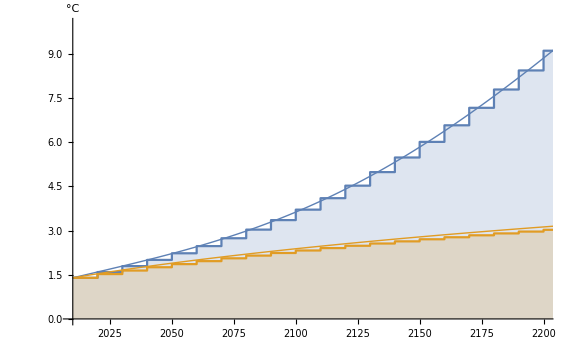

```mathematica
Show[{ListStepPlot[{Table[{2010+10t/1,3Log[(E1[t]+E2[t])/581]/Log[2]},{t,0,Length[Partition[soldec,10]]-2}]/.soldecLF,Table[{2010+10t/1,3Log[(E1[t]+E2[t])/581]/Log[2]},{t,0,Length[Partition[soldec,10]]-2}]/.soldec},PlotRange->Full,Filling->Axis,AxesOrigin->{2010,0},AxesLabel->{None,"°C"},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->20,FontColor->GrayLevel[0.5]} (*,PlotLabels->{Placed["no policy",{.595,.355}],Placed["optimal policy",{.58,.4}]}*)],ListPlot[{Table[{2010+10t/10,3Log[(E1[t]+E2[t])/581]/Log[2]},{t,0,Length[Partition[solann,10]]-2}]/.solannLF,Table[{2010+10t/10,3Log[(E1[t]+E2[t])/581]/Log[2]},{t,0,Length[Partition[solann,10]]-2}]/.solann},PlotRange->Full,Joined->True,PlotStyle->Thick]},PlotRange->{{2010,2200}, {0,10}}]
```

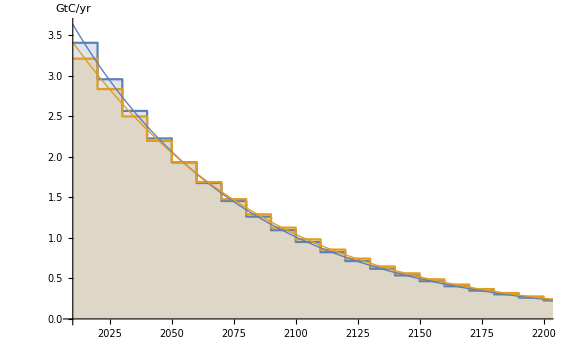

```mathematica
Show[{ListStepPlot[{Table[{2010+10t/1,F[t]/10},{t,0,Length[Partition[soldec,10]]-2}]/.soldecLF,Table[{2010+10t/1,F[t]/10},{t,0,Length[Partition[soldec,10]]-2}]/.soldec},PlotRange->Full,Filling->Axis,AxesOrigin->{2010,0},AxesLabel->{None,"GtC/yr"},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->20}],ListPlot[{Table[{2010+10t/10,F[t] },{t,0,Length[Partition[solann,10]]-2}]/.solannLF,Table[{2010+10t/10,F[t]},{t,0,Length[Partition[solann,10]]-2}]/.solann},PlotRange->Full,Joined->True,PlotStyle->{{Thick}}]},PlotRange->{{2010,2200}, All}]
```

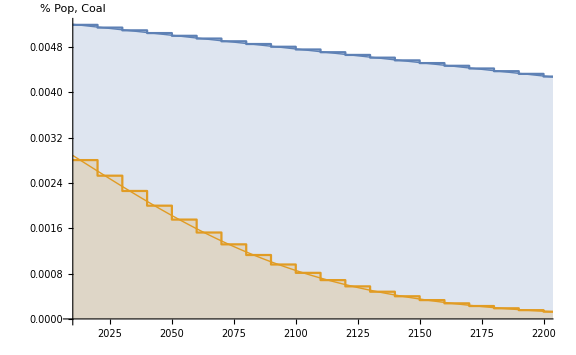

```mathematica
Show[{ListStepPlot[{Table[{2010+10t/1,LC[t]},{t,0,Length[Partition[soldec,10]]-2}]/.soldecLF,Table[{2010+10t/1,LC[t]},{t,0,Length[Partition[soldec,10]]-2}]/.soldec},PlotRange->Full,Filling->Axis,AxesOrigin->{2010,0},AxesLabel->{None,"% Pop, Coal"},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->20}],ListPlot[{Table[{2010+10t/10,LC[t] },{t,0,Length[Partition[solann,10]]-2}]/.solannLF,Table[{2010+10t/10,LC[t]},{t,0,Length[Partition[solann,10]]-2}]/.solann},PlotRange->Full,Joined->True,PlotStyle->{{Thick}}]},PlotRange->{{2010,2200}, All}]
```

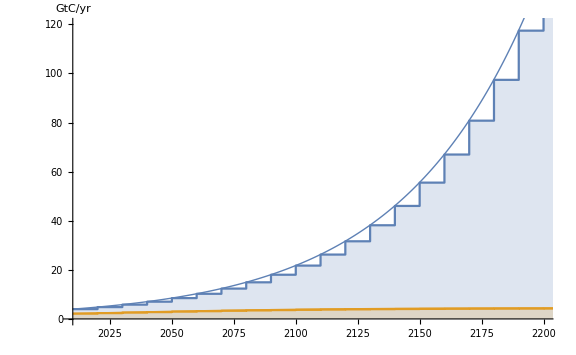

```mathematica
Show[{ListStepPlot[{Table[{2010+10t/1,A20/10 1.02^(10 t)LC[t]/.{A20->7683,A30->1311,ω2->1.02^10,ω3->1.02^10}},{t,0,Length[Partition[soldec,10]]-2}]/.soldecLF,Table[{2010+10t/1,A20/10 1.02^(10 t)LC[t]/.{A20->7683,A30->1311,ω2->1.02^10,ω3->1.02^10}},{t,0,Length[Partition[soldec,10]]-2}]/.soldec},PlotRange->Full,Filling->Axis,AxesOrigin->{2010,0},AxesLabel->{None,"GtC/yr"},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->20}],ListPlot[{Table[{2010+10t/10,A20/10 1.02^t LC[t] /.{A20->7683,A30->1311,ω2->1.02^10,ω3->1.02^10}},{t,0,Length[Partition[solann,10]]-2}]/.solannLF,Table[{2010+10t/10,A20/10 1.02^t LC[t]/.{A20->7683,A30->1311,ω2->1.02^10,ω3->1.02^10}},{t,0,Length[Partition[solann,10]]-2}]/.solann},PlotRange->Full,Joined->True,PlotStyle->{{Thick}}]},PlotRange->{{2010,2200}, {0,120}}]
```

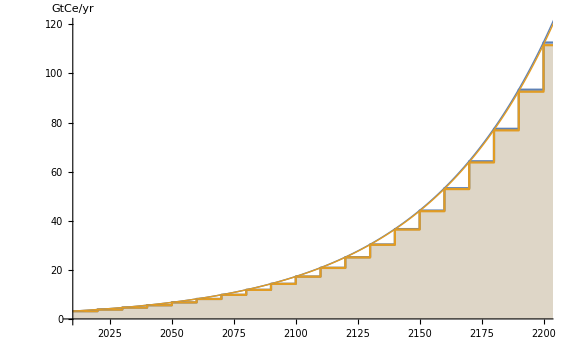

```mathematica
Show[{ListStepPlot[{Table[{2010+10t/1,A30/10 1.02^(10 t)LB[t]/.{A20->7683,A30->1311,ω2->1.02^10,ω3->1.02^10}},{t,0,Length[Partition[soldec,10]]-2}]/.soldecLF,Table[{2010+10t/1,A30/10 1.02^(10 t)LB[t]/.{A20->7683,A30->1311,ω2->1.02^10,ω3->1.02^10}},{t,0,Length[Partition[soldec,10]]-2}]/.soldec},PlotRange->Full,Filling->Axis,AxesOrigin->{2010,0},AxesLabel->{None,"GtCe/yr"},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->20}],ListPlot[{Table[{2010+10t/10,A30/10 1.02^t LB[t] /.{A20->7683,A30->1311,ω2->1.02^10,ω3->1.02^10}},{t,0,Length[Partition[solann,10]]-2}]/.solannLF,Table[{2010+10t/10,A30/10 1.02^t LB[t]/.{A20->7683,A30->1311,ω2->1.02^10,ω3->1.02^10}},{t,0,Length[Partition[solann,10]]-2}]/.solann},PlotRange->Full,Joined->True,PlotStyle->{{Thick}}]},PlotRange->{{2010,2200}, {0,120}}]
```

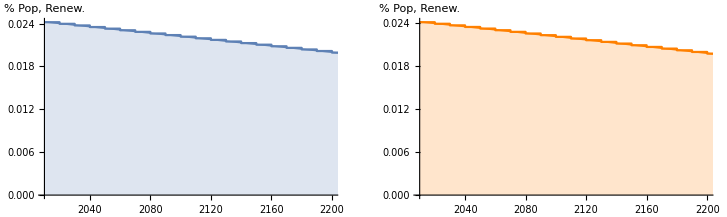

```mathematica
GraphicsGrid[{{Show[{ListStepPlot[{Table[{2010+10t/1,LB[t]},{t,0,Length[Partition[soldec,10]]-2}]/.soldecLF},PlotRange->Full,Filling->Axis,AxesOrigin->{2010,0},AxesLabel->{None,"% Pop, Renew."}],ListPlot[{Table[{2010+10t/10,LB[t] },{t,0,Length[Partition[solann,10]]-2}]/.solannLF},PlotRange->Full,Joined->True,PlotStyle->{{Thick}}]},PlotRange->{{2010,2200}, All}],Show[{ListStepPlot[{Table[{2010+10t/1,LB[t]},{t,0,Length[Partition[soldec,10]]-2}]/.soldec},PlotRange->Full,Filling->Axis,AxesOrigin->{2010,0},PlotStyle->{{Orange}},AxesLabel->{None,"% Pop, Renew."}],ListPlot[{Table[{2010+10t/10,LB[t]},{t,0,Length[Partition[solann,10]]-2}]/.solann},PlotRange->Full,Joined->True,PlotStyle->{{Orange,Thick}}]},PlotRange->{{2010,2200}, All}]}}]
```

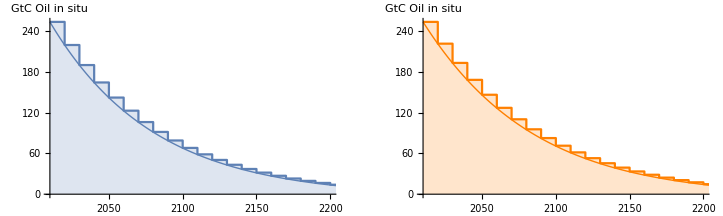

```mathematica
GraphicsGrid[{{Show[{ListStepPlot[{Table[{2010+10t/1,S[t]},{t,0,Length[Partition[soldec,10]]-2}]/.soldecLF},PlotRange->Full,Filling->Axis,AxesOrigin->{2010,0}],ListPlot[{Table[{2010+10t/10,S[t] },{t,0,Length[Partition[solann,10]]-2}]/.solannLF},PlotRange->Full,Joined->True,PlotStyle->{{Thick}}]},PlotRange->{{2010,2200}, All},AxesLabel->{None,"GtC Oil in situ"}],Show[{ListStepPlot[{Table[{2010+10t/1,S[t]},{t,0,Length[Partition[soldec,10]]-2}]/.soldec},PlotRange->Full,Filling->Axis,AxesOrigin->{2010,0},AxesLabel->{None,"GtC Oil in situ"},PlotStyle->{{Orange}}],ListPlot[{Table[{2010+10t/10,S[t]},{t,0,Length[Partition[solann,10]]-2}]/.solann},PlotRange->Full,Joined->True,PlotStyle->{{Orange,Thick}}]},PlotRange->{{2010,2200}, All}]}}]
```

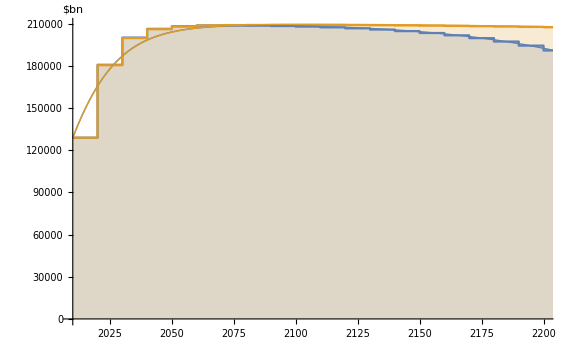

```mathematica
Show[{ListStepPlot[{Table[{2010+10t/1,K[t]},{t,0,Length[Partition[soldec,10]]-2}]/.soldecLF,Table[{2010+10t/1,K[t]},{t,0,Length[Partition[soldec,10]]-2}]/.soldec},PlotRange->Full,Filling->Axis,AxesOrigin->{2010,0},AxesLabel->{None,"$bn"},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->20}],ListPlot[{Table[{2010+10t/10,K[t]},{t,0,Length[Partition[solann,10]]-2}]/.solannLF,Table[{2010+10t/10,K[t]},{t,0,Length[Partition[solann,10]]-2}]/.solann},PlotRange->Full,Joined->True,PlotStyle->{{Thick}}]},PlotRange->{{2010,2200}, All}]
```

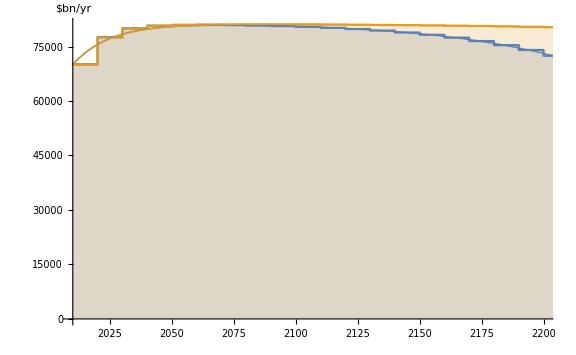

```mathematica
Show[{ListStepPlot[{Table[{2010+10t/1,Y[t]/10},{t,0,Length[Partition[soldec,10]]-2}]/.soldecLF,Table[{2010+10t/1,Y[t]/10},{t,0,Length[Partition[soldec,10]]-2}]/.soldec},PlotRange->Full,Filling->Axis,AxesOrigin->{2010,0},AxesLabel->{None,"$bn/yr"},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->20}],ListPlot[{Table[{2010+10t/10,Y[t]},{t,0,Length[Partition[solann,10]]-2}]/.solannLF,Table[{2010+10t/10,Y[t]},{t,0,Length[Partition[solann,10]]-2}]/.solann},PlotRange->Full,Joined->True,PlotStyle->{{Thick}}]},PlotRange->{{2010,2200},All}]
```

### Model with cap on cumulative emissions

For a model with a cap on cumulative emissions, the equations governing energy use need to be altered. The carbon tax is now is augmented with a component growing at the rate of interest or measured in utils: η0(β γ)^-t(1+β γ (-1+θ-α θ))/(1+β γ (-1+θ))

```mathematica
EnergyEq={φ+η0(β γ)^-t(1+β γ (-1+θ-α θ))/(1+β γ (-1+θ))+((1+β γ (-1+θ-α θ)) μ[t])/(1+β γ (-1+θ))==(κ1 ν F[t]^(-1+ρ))/(κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ),(-1+α+ν)/(-ω^t L[t]+LB[t]+LC[t])==(κ3 ν (A3[t] LB[t])^ρ)/(LB[t] (κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ)),(φ+η0(β γ)^-t(1+β γ (-1+θ-α θ))/(1+β γ (-1+θ))) A2[t]+(-1+α+ν)/(-ω^t L[t]+LB[t]+LC[t])==(κ2 ν (A2[t] LC[t])^ρ)/(LC[t] (κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ)),μ[-1+t]==β γ μ[t]}
```

{((β γ)^-t η0 (1+β γ (-1+θ-α θ)))/(1+β γ (-1+θ))+φ+((1+β γ (-1+θ-α θ)) μ[t])/(1+β γ (-1+θ))==(κ1 ν F[t]^(-1+ρ))/(κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ),(-1+α+ν)/(-ω^t L[t]+LB[t]+LC[t])==(κ3 ν (A3[t] LB[t])^ρ)/(LB[t] (κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ)),(((β γ)^-t η0 (1+β γ (-1+θ-α θ)))/(1+β γ (-1+θ))+φ) A2[t]+(-1+α+ν)/(-ω^t L[t]+LB[t]+LC[t])==(κ2 ν (A2[t] LC[t])^ρ)/(LC[t] (κ1 F[t]^ρ+κ3 (A3[t] LB[t])^ρ+κ2 (A2[t] LC[t])^ρ)),μ[-1+t]==β γ μ[t]}

From Routine which sets final oil stock and the scarcity rent to zero, we can solve for “critical” η0 value of 0.0007844208444091677`. Extra solution around this point are important due to kink.

```mathematica
Clear[sol];sol={};Table[With[{T=40},With[{solution=Flatten[With[{Sys=Flatten[{ηd==η0,φd==φ,S[0]==S0,μ[T]S[T+1]==0,CE[0]==0,Table[Flatten[{EnergyEq,S[t+1]-S[t]+F[t]==0,CE[t+1]==CE[t]+F[t]+A2[t]LC[t]}],{t,0,T}]//Transpose}/.{φ->(ψ(1-(α β γ θ)/(1-β γ (1-θ)))+χ/(1-β γ δ))(Subscript[φ, L]/(1-β γ)+((1-Subscript[φ, L] )Subscript[φ, 0])/(1-β γ ε))}/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.{ω->1.0}/.Param],Vars=Flatten[{Flatten[Table[Transpose[{{S[t],μ[t],F[t],LC[t],LB[t],CE[t]},{S0 (β γ)^t,0.00000001 (β γ)^t,S0/T(β γ)^t,0.000015 (β γ)^(1.5t),0.02(β γ)^t,S0 (1-(β γ)^t)}}],{t,0,T}],1],{{μ[-1],0.0},{S[T+1],0.1,0,1000},{CE[T+1],0.1},{φd,0},{ηd,0}}},1]/.Param},FindRoot[Sys/.Param/.η0->x0,Vars]]]},sol=Append[sol,solution];
{{CE[T],x0},{CE[T],-S[T+1]},{CE[T],μ[0]},{CE[T],F[0]},{CE[T],A20 LC[0]/.Param}}/.Flatten[solution]]],{x0,Flatten[{Table[10^-z,{z,2,9,0.1}],Table[z,{z,.0007,.0009,.000025}](*Table[z,{z,0,.0065,.000065}]*)}]}];
```

#### Figures in carbon budget space

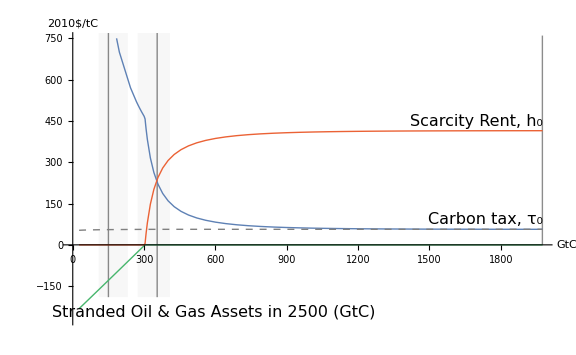

```mathematica
Map[Sort,Transpose[(Thread[{CE[40],{(φd +ηd(β γ)^-t(1+β γ (-1+θ-α θ))/(1+β γ (-1+θ)))Y[t],φd Y[t],-S[41],μ[t] Cons[t]}}]/.{Cons[t_]->(1-(α β γ θ)/(1-β γ (1-θ))) Y[t]}/.{Y[t_]->K[t]^α A[t](ℰ[F[t],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν)} /.{ℰ->((κ1#1^ρ+κ2#2^ρ+κ3#3^ρ)^(1/ρ)&)}/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.t->0/.Thread[{K[0],A[0]}->{K0,A0star}]/.Param/.Param2/.#)&/@sol]];
ListPlot[%,Joined->True,ImageSize->Large,PlotRange->{Full,{-270,750}}, AxesLabel->{"GtC","2010$/tC"},PlotStyle->{Thick,{Thick,Dashed,Gray},{Thick,ColorData[97,"ColorList"][[-1]]},Thick},PlotLabels->{None,Placed["Carbon tax, τ_0",Above],Placed["Stranded Oil & Gas Assets in 2500 (GtC)",{.29,-0.05}],Placed["Scarcity Rent, h_0",Above]},LabelStyle->{FontFamily->"Times",FontSize->16},Prolog->{Opacity[0.03],Rectangle[{109,-190},{232,810}],Rectangle[{273,-190},{409,810}],Opacity[0.45],Line[{{150,-190},{150,810}}],Line[{{355,-190},{355,810}}],Line[{{1975,0},{1975,760}}]},Epilog->{FontFamily->"Times",FontSize->16,Text["1.5°C",{170,860}],Text["2°C",{365,860}],Text["no",{1975,860}],Text["cap",{1975,800}]}]
```

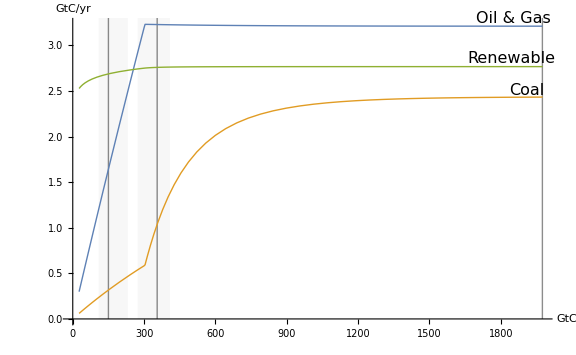

```mathematica
Map[Sort,Transpose[(Thread[{CE[40],1/10{F[0],A2[0] LC[0],A3[0] LB[0]}}]/.{Cons[t_]->(1-(α β γ θ)/(1-β γ (1-θ))) Y[t]}/.{Y[t_]->K[t]^α A[t](ℰ[F[t],A2[t] LC[t],A3[t] LB[t]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν)} /.{ℰ->((κ1#1^ρ+κ2#2^ρ+κ3#3^ρ)^(1/ρ)&)}/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.t->0/.Thread[{K[0],A[0]}->{K0,A0star}]/.Param/.Param2/.#)&/@sol]];
ListPlot[%,Joined->True,ImageSize->Large,PlotRange->Full,PlotStyle->Thick,PlotLabels->{Placed["Oil & Gas",{0.938,1.02}],Placed["Coal",{0.965,1.03}],Placed["Renewable",{0.932,1.35}]},AxesLabel->{"GtC","GtC/yr"}, Prolog->{Opacity[0.03],Rectangle[{109,0},{232,3.4}],Rectangle[{273,0},{409,3.4}],Opacity[0.45],Line[{{150,0},{150,3.4}}],Line[{{355,0},{355,3.4}}],Line[{{1975,0},{1975,3.4}}]},(*Epilog->{FontFamily->"Times",FontSize->16,Text["1.5°C",{170,3.35}],Text["2°C",{375,3.35}]},*)LabelStyle->{FontFamily->"Times",FontSize->16}]
```

#### Computing carbon budget using IPCC table 2.2

Computing cumulative emissions from permanent component. 515 GtC is in line with the 505 GtC of IPCC  ((2250-400)/3.6666).

```mathematica
(684-581)/0.2
```

515.

Using carbon budget from 2010 onward for 1.5°C, 2°C, and 3°C with 33%, 50%, and 66% chance.

```mathematica
{400, 550,850, 1000, 1300, 1500, 2400, 2800, 3250}/3.66666
```

{109.091,150.,231.819,272.728,354.546,409.092,654.547,763.638,886.365}

#### Figure with time profiles for carbon tax for 1.5, 2, and no cap

```mathematica
Clear[soldec];Clear[τset];τset={};
Table[
With[{solution=Flatten[Pick[sol,Table[CE[40]/.x,{x,sol}],Nearest[Table[CE[40]/.Flatten[x],{x,sol}],CEtarget][[1]]]],EnvEq=Thread[{E1[t],E2[t],A[t]}==({E1[t],E2[t],A[t]}/.Flatten[Solve[EqTrans[[{3,4,-1}]],{E1[t],E2[t],A[t]},Reals]])]},
With[{EnvState=Flatten[FindRoot[Flatten[{Thread[{E1[0],E2[0],A[0]}=={E10, E20,A0star}],Table[EnvEq,{t,1,Length[Partition[solution,6]]-1}]}]/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.Param/.solution/.Abar->Abarstar/.Param2,Flatten[Transpose[Table[{{E1[t],E2[t],A[t]},{E10 ω2^t, E20 ω2^t,A0star }/.Param/.Param2},{t,0,Length[Partition[solution,6]]-1}],{1,3,2}],1]]]},
soldec=Flatten[{solution[[-2;;-1]],Transpose[{Partition[solution,6],Partition[EnvState,3],Partition[FindRoot[Flatten[{Thread[{K[0]}=={K0}],Table[{EqTrans[[{1}]],K[t]^α==Y[t]/(A[t](ℰ[𝒮[F[t],S[t]],A2[t] LC[t],ℬ[LB[t],B[t]]])^ν(ω^t L[t]-LB[t]-LC[t])^(1-α-ν))}/.{Cons[t_]->(1-(α β γ θ)/(1-β γ (1-θ))) Y[t]}/.{ℰ->((κ1#1^ρ+κ2#2^ρ+κ3#3^ρ)^(1/ρ)&)}/.{ℬ[LB[t],B[t]]->A3[t] ⅇ^(ϱ(B[t]+B0)) LB[t],D[ℬ[LB[t],B[t]]->A3[t] ⅇ^(ϱ(B[t]+B0)) LB[t],LB[t]]}/.{𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],D[𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],S[t]],D[𝒮[F[t],S[t]]-> ⅇ^(σ(S[t]-S0)) F[t],F[t]]}/.{σ->0,ϱ->0,ξ[t]->0},{t,0,Length[Partition[solution,6]]-1}]}]/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.{ω->1.0}/.Param/.solution/.Abar->Abarstar/.Param2/.EnvState,Flatten[{Transpose[Table[{{K[t],Y[t]},({K0,Y0}/.Param/.Param2)},{t,0,Length[Partition[solution,6]]-1}],{1,3,2}],{{{K[Length[Partition[solution,6]]],0}}}},2]],2]}]}];
τset=Append[τset,Table[(φd +ηd(β γ)^-t(1+β γ (-1+θ-α θ))/(1+β γ (-1+θ)))Y[t]/.{Cons[t_]->(1-(α β γ θ)/(1-β γ (1-θ))) Y[t]},{t,0,19}]/.Param/.soldec]]],{CEtarget,{400, 550,850, 1000, 1300, 1500,10^6  2400,10^6 2800,10^6 3250}/3.66666}];
```

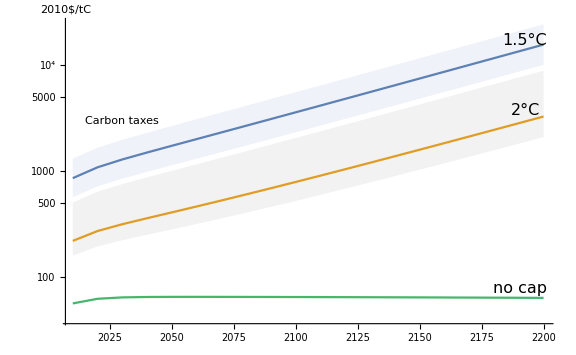

```mathematica
ListLogPlot[τset,Joined->True,PlotRange->Full,PlotStyle->{None,ColorData[97,"ColorList"][[1]],None,None,ColorData[97,"ColorList"][[2]],None,None,ColorData[97,"ColorList"][[-1]],None},Filling->{1->{{3},Lighter[ColorData[97,"ColorList"][[1]],0.9]},4->{{6},{GrayLevel[.95]}},7->{9}},AxesLabel->{None,"2010$/tC"}, PlotLabels->{None,Placed["1.5°C",{0.96,1.03}],None,None,Placed["2°C",{0.961,1.05}],None,None,Placed["no cap",{0.95,2.3}],None},DataRange->{2010,2200},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->16},Epilog->{FontFamily->"Times",FontSize->16,Text["Carbon taxes",{2030,8}]}]
```

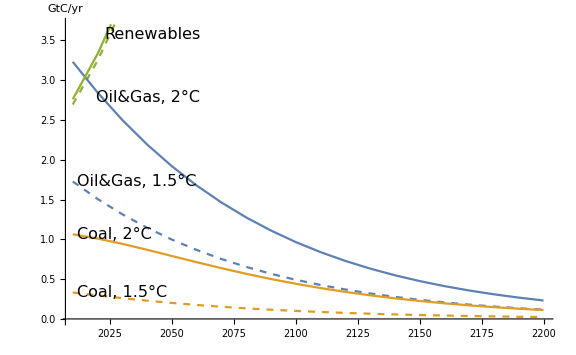

```mathematica
Table[Transpose[Table[1/10{F[t],A2[t] LC[t],A3[t] LB[t]},{t,0,19}]/.Flatten[Pick[sol,Table[CE[40]/.x,{x,sol}],Nearest[Table[CE[40]/.Flatten[x],{x,sol}],CEtarget][[1]]]]/.{L[t_]->L0 γ^t,A2[t_]->A20 ω2^t,A3[t_]->A30 ω3^t}/.Param/.Param2],{CEtarget,{550,1300}/3.66666}];
ListPlot[Flatten[%,1],Joined->True,PlotRange->{Full,{0,3.7}},AxesLabel->{None,"GtC/yr"}, PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashed},{ColorData[97,"ColorList"][[2]],Dashed},{ColorData[97,"ColorList"][[3]],Dashed},ColorData[97,"ColorList"][[1]],{ColorData[97,"ColorList"][[2]]},ColorData[97,"ColorList"][[3]],None},PlotLabels->{Placed["Oil&Gas, 1.5°C",Left],Placed["Coal, 1.5°C",Left],Placed["Renewables",{0.17,0.01}],Placed["Oil&Gas, 2°C",{.16,.85}],Placed["Coal, 2°C",Left],None,None,None,None,None,None,None},DataRange->{2010,2200},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->16}]
```